# Solving OFAST

```mathematica
(*
Copyright (c) 2016 F.X.Coudert& G.Fraux 

Permission is hereby granted,free of charge,to any person obtaining a copy 
of this software and associated documentation files (the "Software"),to deal 
in the Software without restriction,including without limitation the rights 
to use,copy,modify,merge,publish,distribute,sublicense,and/or sell copies of 
the Software,and to permit persons to whom the Software is furnished to do so,
 subject to the following conditions:

The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED "AS IS",WITHOUT WARRANTY OF ANY KIND EXPRESS OR
   IMPLIED INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY, 
    FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL 
   THE AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM,DAMAGES OR OTHER
   LIABILITY, WHETHER IN AN ACTION OF CONTRACT TORT OR OTHERWISE ARISING FROM,
    OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE SOFTWARE.
*)
Get["OFAST`"];
```

```mathematica
(* Values for Cu(dhbc)2(bypy) structure, converted to mol/u.c. *)
KO2 =0.0342924;
NO2=2.67873;
KCO2=0.699231;
NCO2=2.7929;
KCH4=0.134329;
NCH4=2.86018;

DeltaF = -3500;
```

### CH4 / O2

```mathematica
SelectivityAtComposition[yB_] := Table[{pp, SolveOFAST[KCH4, NCH4, KO2, NO2, DeltaF, yB, pp][[1]]}, {pp, 1, 100, 1}]
select01 = SelectivityAtComposition[0.1];
select05 = SelectivityAtComposition[0.5];
select09 = SelectivityAtComposition[0.9];
```

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CH4-O2-0.1.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CH4-O2-0.5.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CH4-O2-0.9.dat".

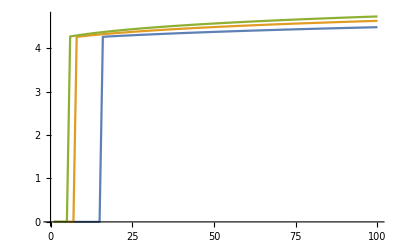

```mathematica
Export["results/OFAST-CH4-O2-0.1.dat", select01];
Export["results/OFAST-CH4-O2-0.5.dat", select05];
Export["results/OFAST-CH4-O2-0.9.dat", select09];
ListLinePlot[{select01, select05,select09}]
```

### CH4 / CO2

```mathematica
SelectivityAtComposition[yB_] := Table[{pp, SolveOFAST[KCH4, NCH4, KCO2, NCO2, DeltaF, yB, pp][[1]]}, {pp, 1, 100, 1}]
select01 = SelectivityAtComposition[0.1];
select05 = SelectivityAtComposition[0.5];
select09 = SelectivityAtComposition[0.9];
```

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CH4-CO2-0.1.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CH4-CO2-0.5.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CH4-CO2-0.9.dat".

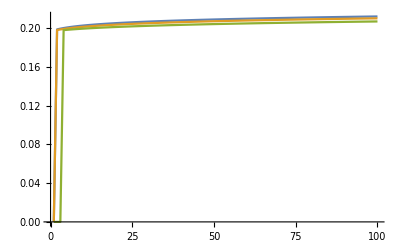

```mathematica
Export["results/OFAST-CH4-CO2-0.1.dat", select01];
Export["results/OFAST-CH4-CO2-0.5.dat", select05];
Export["results/OFAST-CH4-CO2-0.9.dat", select09];
ListLinePlot[{select01, select05,select09}]
```

### CO2 / O2

```mathematica
SelectivityAtComposition[yB_] := Table[{pp, SolveOFAST[KCO2, NCO2, KO2, NO2, DeltaF, yB, pp][[1]]}, {pp, 1, 100, 1}]
select01 = SelectivityAtComposition[0.1];
select05 = SelectivityAtComposition[0.5];
select09 = SelectivityAtComposition[0.9];
```

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CO2-O2-0.1.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CO2-O2-0.5.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-CO2-O2-0.9.dat".

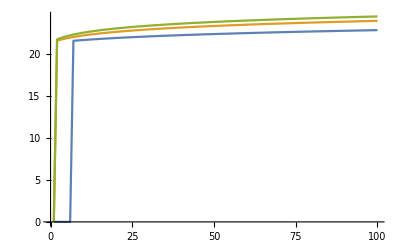

```mathematica
Export["results/OFAST-CO2-O2-0.1.dat", select01];
Export["results/OFAST-CO2-O2-0.5.dat", select05];
Export["results/OFAST-CO2-O2-0.9.dat", select09];
ListLinePlot[{select01, select05,select09}]
```